```mathematica
SeedRandom[1234]; data=Table[Sin[x]+RandomReal[{-0.05,0.05}],{x,0,100,0.04}];
```

```mathematica
training=RandomSample[List/@Most[#]->List@Last[#]&/@(Partition[data,51,1])];
```

```mathematica
net=NetChain[{GatedRecurrentLayer[10,"Dropout"->{"VariationalInput"->0.1,"VariationalState"->0.5}],Tanh,LinearLayer[1]},"Input"->{50,1},"Output"->1]
```

NetChain[<>]

```mathematica
trained=NetTrain[net,training]
```

NetChain[<>]

```mathematica
nl=NestList[Append[Rest[#],trained[#]]&,List/@Sin[ Range[-49*0.04,0,0.04]],1];
```

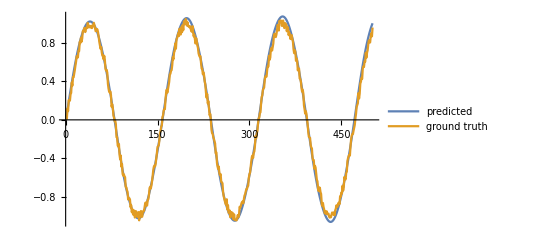

```mathematica
ListPlot[{Flatten@NestList[Append[Rest[#],trained[#]]&,List/@Sin[Range[-49*0.04,0,0.04]]+RandomReal[{-0.05,0.05}],500][[All,-1]],Table[Sin[x]+RandomReal[{-0.05,0.05}],{x,0,500*0.04,0.04}]},Joined->True,PlotLegends->{"predicted","ground truth"}]
```

```mathematica
trained[{{-0.12777409509424595},{0.15981690725050227},{0.43467922920484614},{0.6738046416896878},{0.8570079625835154},{0.9686872077260992},{0.9992062986237391},{0.945771041771658},{0.8127136318287216},{0.6111542467350963},{0.35806531852110113},{0.0748192394425404},{-0.21465182418475384},{-0.48591942273403504},{-0.7161606546683337},{-0.886110510967742},{-0.9816917537422903},{-0.9951803266614782},{-0.9258082120086791},{-0.7797580715318514},{-0.5695597340167056},{-0.3129522077380773},{-0.03132133696340545},{0.25214171717331396},{0.5143952585235498},{0.7344442247881462},{0.8950195272230747},{0.9839039795832403},{0.9948049369548682},{0.927716724209169},{0.7887618629192076},{0.5895446904131978},{0.34609028378218176},{0.07747247695252471},{-0.19574499518422064},{-0.45312163701004293},{-0.6758780934371426},{-0.8482428704167329},{-0.9585140871579997},{-0.9997706690604432},{-0.9701987963944235},{-0.873031187196285},{-0.7161262972860822},{-0.5112395903743637},{-0.2730580744446138},{-0.018081380384810688},{0.23656249976416435},{0.47428076111051853},{0.6800806929965358},{0.8414709848078965}}]
```

{0.92211}

```mathematica
trained[{{0.15981690725050227},{0.43467922920484614},{0.6738046416896878},{0.8570079625835154},{0.9686872077260992},{0.9992062986237391},{0.945771041771658},{0.8127136318287216},{0.6111542467350963},{0.35806531852110113},{0.0748192394425404},{-0.21465182418475384},{-0.48591942273403504},{-0.7161606546683337},{-0.886110510967742},{-0.9816917537422903},{-0.9951803266614782},{-0.9258082120086791},{-0.7797580715318514},{-0.5695597340167056},{-0.3129522077380773},{-0.03132133696340545},{0.25214171717331396},{0.5143952585235498},{0.7344442247881462},{0.8950195272230747},{0.9839039795832403},{0.9948049369548682},{0.927716724209169},{0.7887618629192076},{0.5895446904131978},{0.34609028378218176},{0.07747247695252471},{-0.19574499518422064},{-0.45312163701004293},{-0.6758780934371426},{-0.8482428704167329},{-0.9585140871579997},{-0.9997706690604432},{-0.9701987963944235},{-0.873031187196285},{-0.7161262972860822},{-0.5112395903743637},{-0.2730580744446138},{-0.018081380384810688},{0.23656249976416435},{0.47428076111051853},{0.6800806929965358},{0.8414709848078965},{0.9221096634864807}}]
```

{0.954117}

```mathematica
List/@Sin[2 π Range[-49*0.04,0,0.04]+Cos [Range[-49*0.04,0,0.04]]]
```

{{-0.127774},{0.159817},{0.434679},{0.673805},{0.857008},{0.968687},{0.999206},{0.945771},{0.812714},{0.611154},{0.358065},{0.0748192},{-0.214652},{-0.485919},{-0.716161},{-0.886111},{-0.981692},{-0.99518},{-0.925808},{-0.779758},{-0.56956},{-0.312952},{-0.0313213},{0.252142},{0.514395},{0.734444},{0.89502},{0.983904},{0.994805},{0.927717},{0.788762},{0.589545},{0.34609},{0.0774725},{-0.195745},{-0.453122},{-0.675878},{-0.848243},{-0.958514},{-0.999771},{-0.970199},{-0.873031},{-0.716126},{-0.51124},{-0.273058},{-0.0180814},{0.236562},{0.474281},{0.680081},{0.841471}}